```mathematica
SetDirectory@NotebookDirectory[]
<<"MagnetCode`"
Needs["MathPSfrag`"]
Needs["CustomTicks`"]
mm:=0.001
```

/Users/will/magcode/examples

## Setup

```mathematica
mm:=0.001
tesla:=1
amps:=1
ohms:=1

magnet={
MagnetRadius->5mm,
MagnetLength->10mm,
Magnetisation->1 tesla
}
coil={
CoilRadius->7mm,
CoilLength->20mm,
Current->1 amps,
WireRadius->0.1mm,
WireCoating->0.01mm,
CoilResistance->8ohms
}
CalculateCoilParams[parameters__] := 
  ReleaseHold[{
               Hold@Symbol["CoilRadius"]->CoilRadius,
               Hold@Symbol["CoilThickness"]->CoilThickness,
               Hold@Symbol["CoilTurns"]->TotalTurns,
               Hold@Symbol["CoilLength"]->CoilLength,
               Hold@Symbol["Current"]->Current
              } //. 
  Flatten@{{
    CoilThickness -> ( 2 WireLength (WireRadius+WireCoating)^2 ) /
                                (  π CoilLength (CoilRadius+WireRadius+WireCoating) ) ,
    WireLength -> CoilResistance WireArea / WireResistivity ,
    WireResistivity -> 1.7*10^-8, (* copper *)
    WireArea -> π (WireRadius+WireCoating)^2,
    TotalTurns -> TurnsZ TurnsR,
    TurnsZ -> Round[CoilLength / (2WireRadius+2WireCoating)],
    TurnsR -> Round[CoilThickness / (2WireRadius+2WireCoating)]
    },parameters}//.{cm->0.01,mm->0.001,volts->1,ohms->1}]

CalculateCoilParams[coil]
```

{MagnetRadius→0.005,MagnetLength→0.01,Magnetisation→1}

{CoilRadius→0.007,CoilLength→0.02,Current→1,WireRadius→0.0001,WireCoating→0.00001,CoilResistance→8}

{CoilRadius→0.007,CoilThickness→0.000969041,CoilTurns→364,CoilLength→0.02,Current→1}

## Coil coil filament forces

These equations calculate the forces between two circular coils. The first for coaxial loops, the second including eccentricity. Want to ensure the latter converges to the former for eccentricity converging to zero.

```mathematica
With[{I=1,r=5mm,R=6mm,z=5mm,e=0.1mm},
{CoilCoilForce[I,I,r,R,z],CoilCoilForce[I,I,r,R,z,e]}
]
```

{-7.99888×10^-7,{-7.99631×10^-7,-1.30794×10^-8}}

## Comparison between different methods

Here we hope that a zero-thickness coil and a thin-thickness coil gives similar results.
Eccentricity should result in only small changes in force.

```mathematica
thinvthickparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilLength->20mm,
CoilTurns->400,
Current->1,

Displacement->10mm,
IntegrationPrecision->3,
Verbose->True
};
```

```mathematica
Timing@MagnetCoilForce@{thinvthickparams}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
Babic->False,
CoilThickness->0.1mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm,
Eccentricity->0.1mm
}
```

Coaxial thin coil:

{0.000645,2.60128}

Coaxial thick coil (Babic):

{0.04301,2.58611}

Coaxial thick coil (plain integral):

{0.018044,2.58613}

Eccentric thick coil:

{0.19284,2.53076}

## Comparing Babic’s result with the direct integral

```mathematica
babicparams:={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilThickness->1mm,
CoilLength->20mm,
CoilTurns->400,
Current->1,

Displacement->10mm
}
```

```mathematica
Timing@MagnetCoilForce@{
babicparams,
Babic->True,
Verbose->True,
IntegrationPrecision->3
}
Timing@MagnetCoilForce@{
babicparams,
Babic->False,
Verbose->True,
IntegrationPrecision->3
}
```

Coaxial thick coil (Babic):

{0.039754,2.45444}

Coaxial thick coil (plain integral):

{0.014698,2.45486}

```mathematica
babicAccuracy = Table[
Flatten@{Timing@MagnetCoilForce@{
babicparams,
Babic->True,
IntegrationPrecision->ii
},
Timing@MagnetCoilForce@{
babicparams,
Babic->False,
IntegrationPrecision->ii
}}
,{ii,1,8}]
```

{{0.041141,2.45444,0.01194,2.4744},{0.039156,2.45444,0.013925,2.45486},{0.039581,2.45444,0.013913,2.45486},{0.039456,2.45444,0.020561,2.45444},{0.040023,2.45444,0.024118,2.45444},{0.04183,2.45444,0.036725,2.45444},{0.042254,2.45444,0.059122,2.45444},{0.042717,2.45444,0.142935,2.45444}}

```mathematica
TableForm[Map[InputForm,babicAccuracy,{2}]]
```

0.041140999999981887 | 2.4544407879895993 | 0.01193999999998141 | 2.4744006907978187
0.03915599999999131 | 2.4544407879895993 | 0.013925000000028831 | 2.4548594892044457
0.03958099999999831 | 2.4544407879895993 | 0.013913000000002285 | 2.4548594892044457
0.03945600000002969 | 2.4544438306124783 | 0.020560999999929663 | 2.4544392729491915
0.04002300000001924 | 2.4544438306124783 | 0.024117999999930362 | 2.454441045827852
0.041830000000004475 | 2.4544438296675 | 0.036724999999989905 | 2.454443786446628
0.04225399999995716 | 2.454443830093919 | 0.05912200000000212 | 2.4544438175568843
0.04271699999998191 | 2.4544438300903315 | 0.14293500000002268 | 2.4544438299997147

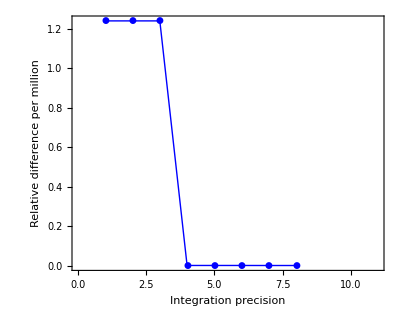
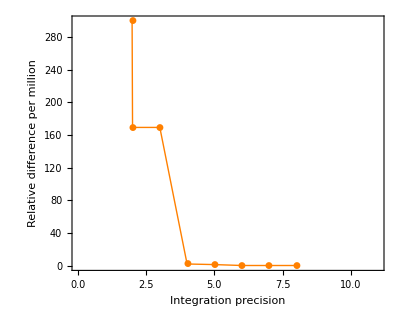

```mathematica
{ListPlot[1000000Abs@{1-babicAccuracy[[All,2]]/babicAccuracy[[-1,2]]},AspectRatio->0.8,PlotStyle->{Blue},PlotRange->{{0,11},Automatic},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}],
ListPlot[1000000Abs@{1-babicAccuracy[[All,4]]/babicAccuracy[[-1,4]]},AspectRatio->0.8,PlotStyle->{Orange},PlotRange->{{0,11},{Automatic,300}},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}]}
```

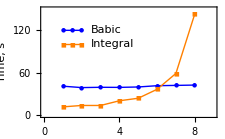

```mathematica
lx:={1,1.5,2,2.5}
ly={120,100};
prectiming=Show@{
ListPlot[1000{babicAccuracy[[All,1]],babicAccuracy[[All,3]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic,6},Joined->True,PlotRange->{{0,9},{0,150}},Frame->True,Axes->False,ImageSize->8 72/2.54,(* 6cm *)FrameLabel->{"Integration precision","Time, s"}],
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange},Joined->True],
Graphics@Text["Babic",{lx[[4]],ly[[1]]},{-1,0}],
Graphics@Text["Integral",{lx[[4]],ly[[2]]},{-1,0}]
}
```

```mathematica
PSfragExport["fig/prec-timing",prectiming,RenumberTags->True]
```

{fig/prec-timing,fig/prec-timing-psfrag.eps,fig/prec-timing-psfrag.tex}

## Comparison with the filament model

### Thin coil

```mathematica
filamentparams={

MagnetRadius->9mm,
MagnetLength->10mm,

(* Turn the magnet into a coil: *)
Magnetisation->1,
MagnetCurrent->Magnetisation MagnetLength/(4π 10^(-7) CoilTurns),

CoilRadius->10mm,
CoilLength->20mm,

CoilTurns->100,
Current->1

};
```

```mathematica
FilamentForce[r_,R_,z_]=-z (1/(√((r+R)^2+z^2)) EllipticK[(4 r R)/((r+R)^2+z^2)]-(r^2+R^2+z^2)/(((r-R)^2+z^2) √((r+R)^2+z^2)) EllipticE[(4 r R)/((r+R)^2+z^2)]);
```

```mathematica
ThinCoilForceFilaments[pp__]:=Hold[Module[
{f1,f2},

f1=Table[-CoilLength/2+(n-1) CoilLength/(CoilTurns-1),{n,1,CoilTurns}];
f2=Table[-MagnetLength/2+(n-1) MagnetLength/(CoilTurns-1),{n,1,CoilTurns}];


4π 10^(-7)Current MagnetCurrent Sum[
FilamentForce[CoilRadius,MagnetRadius,Displacement+z1+z2]
,{z1,f1},{z2,f2}
]
]]//.pp//ReleaseHold
```

Single value test:

```mathematica
ThinCoilForceFilaments@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,CoilThickness->0.5mm,filamentparams}//.filamentparams
```

0.641207

0.650321

0.631622

```mathematica
xmax:=40mm
dx:=1mm
Dx:=2dx
thinthin1=Table[{1000x,ThinCoilForceFilaments@Flatten@{Displacement->x,filamentparams}},{x,dx,xmax,Dx}]
thinthin2=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,filamentparams}},{x,0,xmax,dx}]
thinthin3=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->0.5mm,filamentparams}//.thickfilamentparams},{x,2dx,xmax,Dx}]
(* thinthin4=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->1mm,filamentparams}//.thickfilamentparams},{x,3dx,xmax,Dx}] *)
```

{{1.,0.0601242},{3.,0.194447},{5.,0.377683},{7.,0.546662},{9.,0.626548},{11.,0.640755},{13.,0.591523},{15.,0.458468},{17.,0.302732},{19.,0.208573},{21.,0.149101},{23.,0.109292},{25.,0.0816999},{27.,0.0621022},{29.,0.0479113},{31.,0.0374644},{33.,0.0296594},{35.,0.0237488},{37.,0.0192167},{39.,0.0157008}}

{{0.,0},{1.,0.0617701},{2.,0.127027},{3.,0.199931},{4.,0.285967},{5.,0.388234},{6.,0.485894},{7.,0.557904},{8.,0.606734},{9.,0.636742},{10.,0.650321},{11.,0.648296},{12.,0.630124},{13.,0.593702},{14.,0.534991},{15.,0.451883},{16.,0.365837},{17.,0.298198},{18.,0.246494},{19.,0.206041},{20.,0.173736},{21.,0.147542},{22.,0.126058},{23.,0.108278},{24.,0.0934538},{25.,0.0810169},{26.,0.0705252},{27.,0.0616309},{28.,0.0540568},{29.,0.0475799},{30.,0.0420193},{31.,0.0372275},{32.,0.0330836},{33.,0.0294876},{34.,0.0263568},{35.,0.0236226},{36.,0.0212272},{37.,0.0191227},{38.,0.0172684},{39.,0.01563},{40.,0.0141787}}

{{2.,0.127705},{4.,0.283882},{6.,0.470408},{8.,0.58804},{10.,0.631622},{12.,0.612129},{14.,0.520928},{16.,0.365937},{18.,0.25015},{20.,0.177443},{22.,0.129293},{24.,0.0961637},{26.,0.0727626},{28.,0.0558952},{30.,0.0435295},{32.,0.0343271},{34.,0.0273848},{36.,0.0220809},{38.,0.0179809},{40.,0.0147766}}

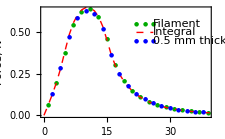

```mathematica
lx:={22,24,26}
ly=Table[i,{i,0.55,0.4,-0.05}];
styles={Darker[Green],{Dashed, Red},Blue,Orange};
joined={False,True,False};
markers={{Automatic,6},None,{Automatic,6}};

compareThinPlot=Show@{
ListPlot[{thinthin1},PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧,
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"}],
ListPlot[{thinthin2},PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[{thinthin3},PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[{thinthin4},PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}}}
,PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧],
ListPlot[
{{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[
{{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}}
,PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[
{{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}}
,PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" 0.5 mm thick",{lx[[3]],ly[[3]]},{-1,0}]
(*Graphics@Text[" 1 mm thick",{lx[[3]],ly[[4]]},{-1,0}]*)
}
```

```mathematica
PSfragExport["fig/thin-compare",compareThinPlot];
```

### Thick coil

```mathematica
thickfilamentparams:={

Displacement->10mm,
MagnetRadius->9mm,
MagnetLength->10mm,

(* Turn the magnet into a coil: *)
MagnetCurrent->Magnetisation MagnetLength/(4π 10^(-7) CoilTurns),
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->CoilTurnsR CoilTurnsZ,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1

}
```

```mathematica
ThickCoilForceFilaments[pp__]:=Hold[Module[
{fr,f1,f2},

fr=CoilRadius+Table[(n-1) (CoilThickness)/(CoilTurnsR-1),{n,1,CoilTurnsR}];
f1=Table[-CoilLength/2+(n-1) CoilLength/(CoilTurnsZ-1),{n,1,CoilTurnsZ}];
f2=Table[-MagnetLength/2+(n-1) MagnetLength/(CoilTurns-1),{n,1,CoilTurns }];

4π 10^(-7)Current MagnetCurrent Sum[
FilamentForce[rr,MagnetRadius,Displacement+z1+z2]
,{rr,fr},{z1,f1},{z2,f2}
]
]]//.pp//ReleaseHold

ThickCoilForceShell[pp__]:=(Hold[Module[{fr},
fr=CoilRadius+
(Hold@Table[(n-1) (CoilThickness)/(CoilTurnsR-1),{n,1,CoilTurnsR}]//.pp)//ReleaseHold;
 Sum[
MagnetCoilForce@Flatten@{CoilRadius->(rr//.pp),CoilThickness->0,pp}
,{rr,fr}
]/(CoilTurnsR//.pp)
]]//ReleaseHold)//.pp
```

```mathematica
Print["Zero coil thickness: (filament, shell)"]
Timing@ThinCoilForceFilaments@thickfilamentparams
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,thickfilamentparams}//.thickfilamentparams

Print["Non-zero coil thickness: (filament, shell, integral, babic)"]
Timing@ThickCoilForceFilaments@thickfilamentparams
Timing@ThickCoilForceShell@thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Babic->False}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Babic->True}//.thickfilamentparams
```

Zero coil thickness: (filament, shell)

{0.369784,0.641207}

{0.000654,0.650321}

Non-zero coil thickness: (filament, shell, integral, babic)

{0.366633,0.473645}

{0.002965,0.497669}

{0.013386,0.49944}

{0.04143,0.493784}

```mathematica
xmax:=40mm
dx:=1.5mm
Dx:=2dx
thinthick1=Table[{1000x,ThickCoilForceFilaments[Flatten@{Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,0dx,xmax,dx}]
thinthick2=Table[{1000x,ThickCoilForceShell[Flatten@{Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,1dx,xmax,Dx}]
thinthick3=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Babic->False,IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,2dx,xmax,Dx}]
thinthick4=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Babic->True,IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,0,xmax,dx}]
```

{{0.,-1.06581×10^-17},{1.5,0.0761861},{3.,0.156069},{4.5,0.243116},{6.,0.3348},{7.5,0.408819},{9.,0.456298},{10.5,0.478114},{12.,0.475077},{13.5,0.447058},{15.,0.394123},{16.5,0.32498},{18.,0.26358},{19.5,0.213897},{21.,0.174231},{22.5,0.142632},{24.,0.117407},{25.5,0.0971951},{27.,0.0809227},{28.5,0.0677554},{30.,0.0570446},{31.5,0.0482853},{33.,0.0410839},{34.5,0.0351321},{36.,0.0301876},{37.5,0.0260592},{39.,0.0225952}}

{{1.5,0.0865854},{4.5,0.27504},{7.5,0.441957},{10.5,0.499736},{13.5,0.449461},{16.5,0.314449},{19.5,0.206902},{22.5,0.138305},{25.5,0.0945124},{28.5,0.0660665},{31.5,0.0472019},{34.5,0.0344233},{37.5,0.0255863}}

{{3.,0.178854},{6.,0.367523},{9.,0.480651},{12.,0.480759},{15.,0.384914},{18.,0.25727},{21.,0.170246},{24.,0.114832},{27.,0.0792315},{30.,0.0559155},{33.,0.040316},{36.,0.0296551},{39.,0.0222187}}

{{0.,0},{1.5,0.0875787},{3.,0.178845},{4.5,0.275189},{6.,0.367508},{7.5,0.437844},{9.,0.480584},{10.5,0.495865},{12.,0.484194},{13.5,0.446026},{15.,0.384878},{16.5,0.316759},{18.,0.257311},{19.5,0.208938},{21.,0.17026},{22.5,0.139438},{24.,0.114831},{25.5,0.095111},{27.,0.0792305},{28.5,0.0663759},{30.,0.0559149},{31.5,0.047356},{33.,0.0403157},{34.5,0.034494},{36.,0.0296549},{37.5,0.0256124},{39.,0.0222186}}

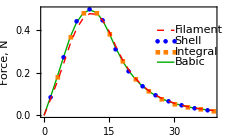

```mathematica
lx:={26,28,30}
ly=Table[i,{i,0.4,0.25,-0.05}];
comparePlot=Show@{
ListPlot[{thinthick4},Joined->True,PlotStyle->{Darker[Green]},
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"}],
ListPlot[{thinthick2,thinthick3},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
ListPlot[{thinthick1},Joined->True,PlotStyle->{Dashed,Red}],
ListPlot[{
{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},
{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}
},Joined->True,PlotStyle->{{Dashed,Red},{Dashing[1],Darker[Green]}}],
ListPlot[{
{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}},
{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}
},PlotMarkers->{Automatic,6},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Shell",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[3]]},{-1,0}],
Graphics@Text[" Babic",{lx[[3]],ly[[4]]},{-1,0}]}
```

```mathematica
PSfragExport["fig/thickthin-compare",comparePlot];
```

## Eccentricity

```mathematica
param={
MagnetRadius->5 mm,
MagnetLength->10 mm,
Magnetisation->1,
CalculateCoilParams@{
CoilRadius ->7 mm,
CoilLength-> 10mm,  
Current->3amps,
WireRadius->0.1mm,
WireCoating->0mm,
CoilResistance->8ohms
},
IntegrationPrecision->3
};
```

```mathematica
{Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0mm}],{x,0mm,30mm}],
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0.1mm}],{x,0mm,30mm}]}
```

$Aborted

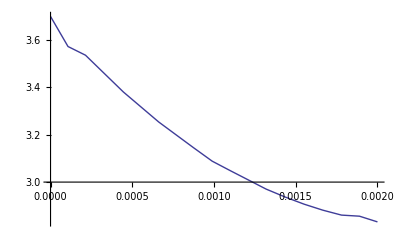

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->7.5mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```

Old:

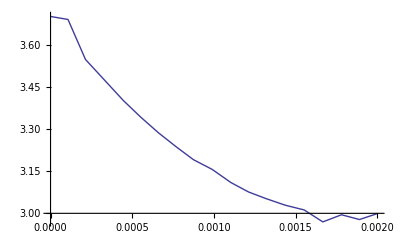

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->7.5mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```